```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
nnoise=Import["ansatz_artificial_nnoise.csv"];
```

```mathematica
noise=Import["ansatz_artificial_noise.csv"];
```

```mathematica
noise[[2;;,2]]
```

{0.65,0.7,0.6,0.55,0.5,0.7,0.55,0.65,0.65,0.55,0.55,0.7,0.55,0.5,0.55,0.55,0.75,0.55,0.55,0.75,0.7,0.6,0.65,0.65,0.7,0.5,0.5}

```mathematica
StandardDeviation[y]
```

0.0749016

```mathematica
x=noise[[2;;,1]];
y=nnoise[[2;;,1]];
```

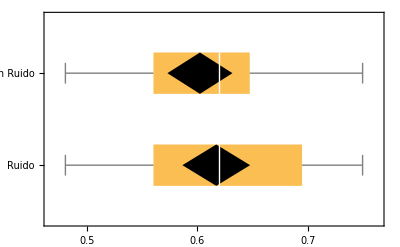

```mathematica
graf=BoxWhiskerChart[{x,y},{"Diamond",{"MeanDiamond",1,Black}},BarOrigin->Right,ChartLabels->{"Ruido","Sin Ruido"},ScalingFunctions->"Reverse"]
```

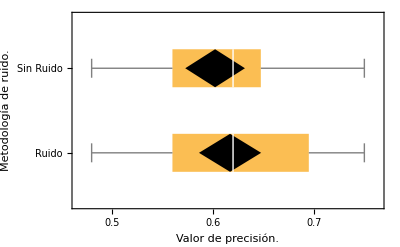

```mathematica
Show[graf,FrameLabel->{{RawBoxes[RowBox[{"Metodología"," ","de"," ",RowBox[{"ruido","."}]}]],None},{RawBoxes[RowBox[{"Valor"," ","de"," ",RowBox[{"precisión","."}]}]],HoldForm[Distribución de la ejecución VQC ANSATZ]}},PlotLabel->None,LabelStyle->{13,GrayLevel[0]}, ImageSize->Full]
```

```mathematica
Export["distributions_artificial_ansatz.pdf",%]
```

distributions_artificial_ansatz.pdf

```mathematica
With[
{α=0.05,x=noise[[2;;,2]],
y=nnoise[[2;;,2]]},
KolmogorovSmirnovTest[x,y,"TestDataTable", SignificanceLevel->α]]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.148148 | 0.742543

```mathematica
With[
{α=0.05,x=noise[[2;;,2]],
y=nnoise[[2;;,2]]},
SignedRankTest[{x,y}]]
```

0.443993

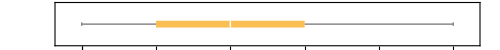

```mathematica
With[{data=nnoise[[2;;,2]]},
{q1,median,q3}=N[Quartiles[data]];
iqr=q3-q1;
bw1=BoxWhiskerChart[data,{"Outliers",{"Outliers","●"},{"FarOutliers","○"}},AspectRatio->1/10,ImageSize->500,BarOrigin->Left,GridLines->{{{q3+1.5iqr,Dashed},{q3+3iqr,Dashed}},None},
FrameTicks->{{None,None},{data,{{q1,"q1"},{q3,"q3"},{q3+1.5iqr,"near"},{q3+3iqr,"far"}}}}]]
```

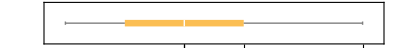

```mathematica
Show[bw1,ImageSize->Full]
```

```mathematica
_
```

_

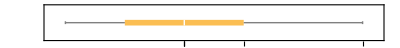

```mathematica
Show[bw1,FrameLabel->{{None,None},{RawBoxes[RowBox[{"Valor"," ","de"," ",RowBox[{"precisión","."}]}]],None}},PlotLabel->HoldForm[Distribución por cuartil. (Sin ruido)],LabelStyle->{13,GrayLevel[0]}, ImageSize->Full]
```

```mathematica
Export[ "distribution_q_ansatz_nnoise_artificial.pdf",%]
```

distribution_q_ansatz_nnoise_artificial.pdf

```mathematica
SystemOpen["img.pdf"]
```

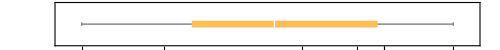

```mathematica
With[{data=noise[[2;;,1]]},
{q1,median,q3}=N[Quartiles[data]];
iqr=q3-q1;
bw2=BoxWhiskerChart[data,{"Outliers",{"Outliers","●"},{"FarOutliers","○"}},AspectRatio->1/10,ImageSize->500,BarOrigin->Left,GridLines->{{{q3+1.5iqr,Dashed},{q3+3iqr,Dashed}},None},
FrameTicks->{{None,None},{data,{{q1,"q1"},{q3,"q3"},{q3+1.5iqr,"near"},{q3+3iqr,"far"}}}}]]
```

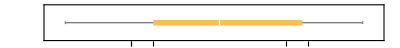

```mathematica
Show[bw2,FrameLabel->{{None,None},{RawBoxes[RowBox[{"Valor"," ","de"," ",RowBox[{"precisión","."}]}]],None}},PlotLabel->HoldForm[Distribución por cuartil. (Ruido de Pauli)],LabelStyle->{13,GrayLevel[0]}, ImageSize->Full]
```

```mathematica
Export[ "distribution_q_ansatz_noise_artificial.pdf",%]
```

distribution_q_ansatz_noise_artificial.pdf

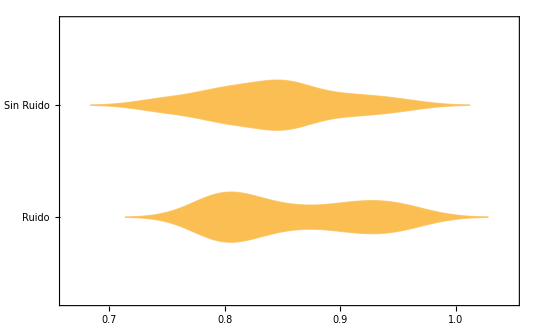

```mathematica
DistributionChart[{x,y},BarOrigin->Right,ChartLabels->{"Ruido","Sin Ruido"},ScalingFunctions->"Reverse"]
```